```mathematica
ResourceFunction["MaTeXInstall"][];
ConfigureMaTeX["pdfLaTeX" -> "/usr/local/bin/pdflatex"];
```

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}"}]
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{color}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

## Energy control

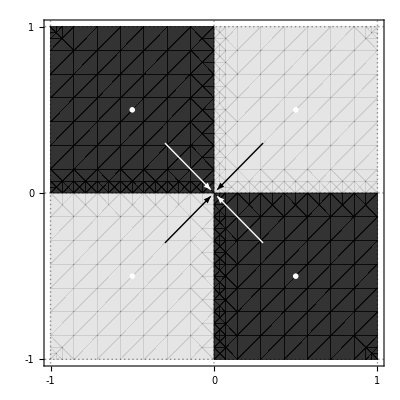

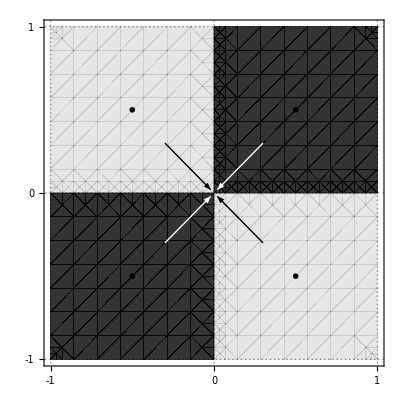

```mathematica
energyControl1 = ContourPlot[x*y, {x, -1, 1}, {y, -1, 1},
Contours->1,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotRange->{1, -1},
FrameLabel ->{MaTeX["\\dot \\theta",Magnification->2],MaTeX[ "E",Magnification->2]},
FrameTicks->{{0, -1, 1}, {0, -1, 1}},
GridLines->{{0, -1, 1}, {0, -1, 1}},
Method->{"TransparentPolygonMesh"->True},
Epilog->{
White,
Text[MaTeX["+a_{max}",Magnification->2], {.5, .5}],Text[MaTeX["+a_{max}",Magnification->2], {-.5, -.5}],
Text[MaTeX["\\color{white}-a_{max}",Magnification->2], {.5, -.5}],
Text[MaTeX["\\color{white}-a_{max}",Magnification->2], {-.5, .5}],
Arrow[{{-.3, .3}, {-.02, .02}}],
Arrow[{{.3, -.3}, {.02, -.02}}],
Black,
Arrow[{{.3, .3}, {.02, .02}}],
Arrow[{{-.3, -.3}, {-.02, -.02}}]
}
]

energyControl2 = ContourPlot[-x*y, {x, -1, 1}, {y, -1, 1},
Contours->1,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotRange->{1, -1},
FrameLabel ->{MaTeX["\\dot \\theta",Magnification->2],MaTeX[ "E",Magnification->2]},
FrameTicks->{{0, -1, 1}, {0, -1, 1}},
GridLines->{{0, -1, 1}, {0, -1, 1}},
Method->{"TransparentPolygonMesh"->True},
Epilog->{
Black,
Text[MaTeX["+a_{max}",Magnification->2], {-.5, .5}],Text[MaTeX["+a_{max}",Magnification->2], {.5, -.5}],
Text[MaTeX["\\color{white}-a_{max}",Magnification->2], {.5, .5}],
Text[MaTeX["\\color{white}-a_{max}",Magnification->2], {-.5, -.5}],
Arrow[{{-.3, .3}, {-.02, .02}}],
Arrow[{{.3, -.3}, {.02, -.02}}],
White,
Arrow[{{.3, .3}, {.02, .02}}],
Arrow[{{-.3, -.3}, {-.02, -.02}}]
}
]
```

```mathematica
Export[NotebookDirectory[]<>"../energy-control1.pdf",energyControl1,"PDF"]
Export[NotebookDirectory[]<>"../energy-control2.pdf",energyControl2,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../energy-control1.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../energy-control2.pdf

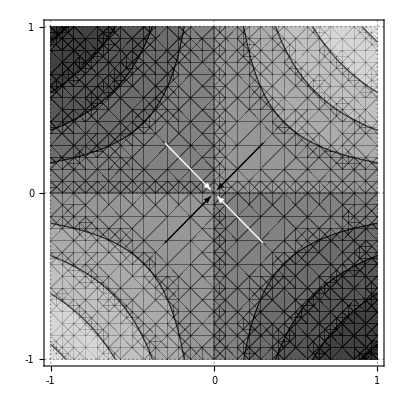

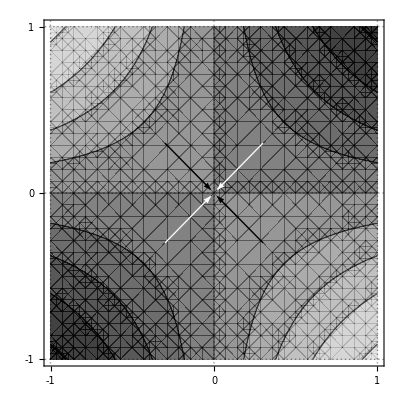

```mathematica
energyControl3 = ContourPlot[Tanh[x*y], {x, -1, 1}, {y, -1, 1},
Contours->10,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotRange->{1, -1},
FrameLabel ->{MaTeX["\\dot \\theta",Magnification->2],MaTeX[ "E",Magnification->2]},
FrameTicks->{{0, -1, 1}, {0, -1, 1}},
GridLines->{{0, -1, 1}, {0, -1, 1}},
Method->{"TransparentPolygonMesh"->True},
Epilog->{
White,
Arrow[{{-.3, .3}, {-.02, .02}}],
Arrow[{{.3, -.3}, {.02, -.02}}],
Black,
Arrow[{{.3, .3}, {.02, .02}}],
Arrow[{{-.3, -.3}, {-.02, -.02}}]
}
]

energyControl4 = ContourPlot[-Tanh[x*y], {x, -1, 1}, {y, -1, 1},
Contours->10,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotRange->{1, -1},
FrameLabel ->{MaTeX["\\dot \\theta",Magnification->2],MaTeX[ "E",Magnification->2]},
FrameTicks->{{0, -1, 1}, {0, -1, 1}},
GridLines->{{0, -1, 1}, {0, -1, 1}},
Method->{"TransparentPolygonMesh"->True},
Epilog->{
Black,
Arrow[{{-.3, .3}, {-.02, .02}}],
Arrow[{{.3, -.3}, {.02, -.02}}],
White,
Arrow[{{.3, .3}, {.02, .02}}],
Arrow[{{-.3, -.3}, {-.02, -.02}}]
}
]
```

```mathematica
Export[NotebookDirectory[]<>"../energy-control3.pdf",energyControl3,"PDF"]
Export[NotebookDirectory[]<>"../energy-control4.pdf",energyControl4,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../energy-control3.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../energy-control4.pdf

## Cogging Torque

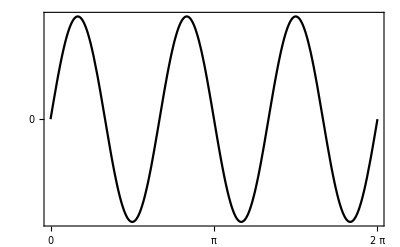

```mathematica
coggingTorque = Plot[Sin[3*x], {x, 0, 2Pi},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotLegends->{Placed[LineLegend[{MaTeX[TeXForm[Subscript[τ, c]],Magnification->2]}], {.85, .9}]},
PlotRange->{5, -5},
FrameLabel ->{MaTeX["\\text{Angolo}",Magnification->1.5], MaTeX["\\text{Coppia}",Magnification->1.5]},
FrameTicks->{{{0}, None}, {{0, Pi, 2Pi}, None}},
GridLines->{{0, Pi, 2Pi}, {0}}
]
```

```mathematica
Export[NotebookDirectory[]<>"../cogging-torque.pdf",coggingTorque,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../cogging-torque.pdf